## Lesson

Test for equality:

```mathematica
1==2
```

False

Test whether less:

```mathematica
1<2
```

True

Test whether more:

```mathematica
1>2
```

False

Test whether less or equal:

```mathematica
1<=2
```

True

Test whether more or equal:

```mathematica
1>=2
```

False

If statement:

```mathematica
If[2+2==4,x,y]
```

x

Select elements which meet a condition:

```mathematica
Select[{1,2,3,4,5,6,7},#>3&]
```

{4,5,6,7}

Test if even:

```mathematica
EvenQ[4]
```

True

Test if even:

```mathematica
EvenQ[4]
```

True

Test if odd:

```mathematica
OddQ[4]
```

False

Test if integer:

```mathematica
IntegerQ[4]
```

True

Test if prime:

```mathematica
PrimeQ[4]
```

False

Test if letter:

```mathematica
LetterQ["4"]
```

False

Test if member of list:

```mathematica
MemberQ[{1,2,3},2]
```

True

Test whether image is an example of a category:

```mathematica
ImageInstanceQ[-Graphics-, Entity["Species","Species:FelisCatus"]]
```

True

## Questions

Q1. Test whether 123^321 is greater than 456^123.

```mathematica
123^321>456^123
```

True

Q2. Get a list of numbers up to 100 whose digits add up to less than 5.

```mathematica
Select[Range[100],Total[IntegerDigits[#]]<5&]
```

{1,2,3,4,10,11,12,13,20,21,22,30,31,40,100}

Q3. Make a list of the first 20 integers, with prime numbers styled red.

```mathematica
If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Q4. Find words in WordList[ ] that both begin and end with the letter “p”.

```mathematica
Select[WordList[],StringTake[#,-1]==StringTake[#,1]=="p"&]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,peep,penmanship,pep,pickup,pileup,pip,plop,plump,polyp,pomp,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

Q5. Make a list of the first 100 primes, keeping only ones whose last digit is less than 3.

```mathematica
Select[Prime[Range[100]],Mod[#,10]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

Q6. Find Roman numerals up to 100 that do not contain “I”.

```mathematica
Select[RomanNumeral[Range[100]],!MemberQ[Characters[#],"I"]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

Q7. Get a list of Roman numerals up to 1000 that are palindromes.

```mathematica
Select[RomanNumeral[Range[1000]],#==StringReverse[#]&]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

Q8. Find names of integers up to 100 that begin and end with the same letter.

```mathematica
Select[IntegerName[Range[100]],StringTake[#,-1]==StringTake[#,1]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

Q9. Get a list of words longer than 15 characters from the Wikipedia article on words.

```mathematica
Select[TextWords[WikipediaData["words"]],StringLength[#]>15&]
```

{yibi-jarran-gabun,yibi-gabun-jarran,orthographically,multiple-morpheme,Proto-Indo-European,978-0-08-044854-1}

Q10. Starting from 1000, divide by 2 if the number is even, and compute 3#+1& if the number is odd; do this repeatedly 200 times (Collatz problem).

```mathematica
Nest[If[EvenQ[#],#/2,3#+1]&,1000,200]
```

2

Q11. Make a word cloud of 5-letter words in the Wikipedia article on computers.

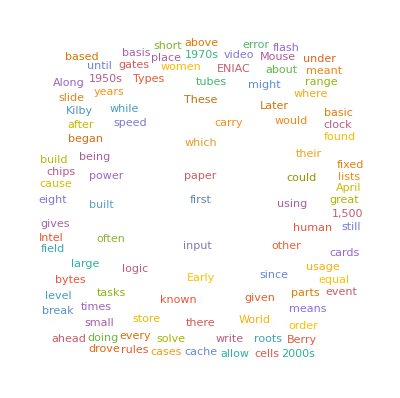

```mathematica
WordCloud[Select[TextWords[WikipediaData["computers"]],StringLength[#]==5&]]
```

Q12. Find words in WordList[ ] whose first 3 letters are the same as their last 3 read backward, but where the whole string is not a palindrome.

```mathematica
Select[WordList[],StringLength[#]>=3&&#!=StringReverse[#]&&StringReverse[StringTake[#,-3]]==StringTake[#,3]&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

Q13. Find all 10-letter words in WordList[ ] for which the total of LetterNumber values is 100.

```mathematica
Select[WordList[],Total[LetterNumber[Characters[#]]]==100&]
```

{acclimation,accumulate,acknowledge,acquitted,adulthood,affectation,alienation,amiableness,analysis,annually,answerable,anterior,apoplectic,appertain,appointed,apropos,aquamarine,archdiocesan,asbestos,attitude,autoclave,automated,avocation,awfully,beetroot,benediction,bettering,bewitching,bipartite,birthmark,blissful,botanist,bouillon,boulevard,boundary,boycott,breviary,bronchus,browser,burnished,cacophony,candidature,cardiograph,carouser,carpenter,carroty,censurable,ceramicist,chastening,chimpanzee,chromium,clinically,clockwise,clotting,coatroom,collecting,cometary,companion,comport,concavely,condensate,confabulate,congenital,congress,conjoint,conjugated,conjunct,connivance,contented,cookout,corridor,costumed,couchette,coverlet,coyness,creosote,crudity,culture,curettage,cutout,cysteine,debarkation,declarative,declension,decorous,deliquesce,delivery,demobilize,demodulate,denominate,depletion,dewberry,diagonally,digestive,dinginess,disarranged,discernible,discipline,discommode,discredited,disjoint,dispraise,distrait,divinely,dooryard,doubleheader,drizzle,dumbfound,duologue,ebullient,egoistical,elsewhere,emasculate,embodiment,emendation,empathetic,encrust,epitaxy,espouse,eulogize,eventual,excellent,excoriate,falseness,fatalistic,fatherhood,ferryman,finitely,fluorine,flurry,forefoot,forewarn,forgiver,forsaking,fountain,frisson,gauntlet,geographer,gladiolus,glissando,glutamate,godparent,grandaunt,grappling,grouper,grumpy,harmonics,healthily,hemoglobin,hirsute,hobbyist,hollering,holograph,honeycomb,honoring,hospital,hotness,imbroglio,immature,impaction,imported,impotence,inadequacy,inapplicable,inefficient,inflation,ingrown,innately,innovate,inoculate,insecticide,intellect,interbreed,interfere,irritate,jailhouse,judiciary,kibitzer,knothole,landholding,landscaping,largeness,leveraging,liberalism,liberator,lightning,likelihood,limpidly,litotes,lubricant,macrocosm,magnetize,martinet,martingale,matchless,matchmaking,maximize,meatpacking,mercantile,mercurial,merganser,meridional,merrily,midpoint,mirrored,misdirect,missus,molecular,morphemic,moussaka,mummify,nastily,neoclassic,nestling,neuronal,nihilist,ninepins,nonhuman,nostalgic,notional,numeracy,nutty,obscenely,offhandedly,operetta,ornament,outflank,outlier,outlined,outrank,outset,overboard,palpitate,paramecium,pasture,pathless,personage,personal,perturb,phagocyte,phlebitis,pianistic,pilaster,pistachio,plastered,plebiscite,plummet,plummy,postdate,posting,postpaid,potbellied,pounding,pouring,prevent,primary,printer,producer,profuse,progeny,publicly,pumpkin,pursue,putter,pyridine,quadrangle,quarry,quarter,quicklime,radiocarbon,raillery,ravisher,receptor,reciprocal,redeploy,refinery,reflation,regimented,regroup,reimpose,renovate,repress,reprint,reprobate,reputable,reschedule,researcher,reshuffle,resolved,restore,retiring,reversal,riverbank,roadster,roomful,roommate,ruction,sagebrush,saintlike,saintly,salacious,savory,scoreboard,scrapbook,scrummage,sculpted,scuttle,selective,self-defense,semaphore,semitone,septicemia,services,session,shadowing,shakedown,shakeout,shattered,shibboleth,shipyard,shooter,shortcake,shrieking,sightly,simulate,sleepyhead,smitten,snobbery,socialism,soughing,sparkler,spirited,splashy,spyhole,squint,stagecraft,stalemated,starfish,starling,status,strangled,stress,striker,subsume,sucrose,surcharge,surely,sweetened,sweptback,swimmer,swollen,syndicate,tailspin,telephone,telescope,temperance,temporal,tensely,tetanus,thalidomide,therefore,thickening,thievish,thirty,thorny,threatened,thumbnail,tinkerer,towards,traction,trademarked,transect,transom,trembling,triplet,tropics,truism,tularemia,tuppence,turkey,turnoff,twisted,unaltered,unavailable,unbounded,unbridgeable,unbroken,uncombined,underdone,underlay,undress,unequaled,unfasten,unfreeze,unhorse,unkempt,unlighted,unmanly,unmatchable,unmodified,unrelated,unwearied,urbanized,urticaria,useless,utensil,variety,varnished,venation,verbalize,vinous,vouchsafe,waterbird,Wednesday,whenever,whirling,whiskey,wholesale,whooper,writing,yarrow}

## Extended Questions

+Q1. Make a table of integers up to 25 where every integer ending in 3 is replaced with 0.

```mathematica
If[IntegerDigits[#][[-1]]==3,0,#]&/@Range[25]
```

{1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25}

+Q2. Use Table and If to make a 5×5 array that is 1 on its leading diagonal, and 0 otherwise.

```mathematica
Table[If[i==j,1,0],{i,5},{j,5}]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

+Q3. Get a list of numbers up to 1000 that are equal to 1 mod both 7 and 8.

```mathematica
Select[Range[1000],Mod[#,7]==Mod[#,8]==1&]
```

{1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953}

+Q4. Make a list of numbers up to 100, where multiples of 3 are replaced by Black, multiples of 5 by White and multiples of 3 and 5 by Red.

```mathematica
Table[If[Mod[n,15]==0,Red,If[Mod[n,5]==0,White,If[Mod[n,3]==0,Black,n]]],{n,100}]
```

{1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]}

+Q5. Use Select to get a list of planets whose mass is larger than Earth.

```mathematica
Select[EntityList[EntityClass["Planet",All]],#["Mass"]>Entity["Planet","Earth"]["Mass"]&]
```

{Jupiter,Saturn,Uranus,Neptune}

+Q6. Make a 50×50 array plot in which a square at position i, j is black if Mod[i, j]==0.

```mathematica
ArrayPlot[Table[Mod[i,j]==0,{i,50},{j,50}]/.{True->1,False->0}]
```

-Graphics-

+Q7. Make a 100×100 array plot in which a square is black if the values of both its x and y positions do not contain a 5.

```mathematica
ArrayPlot[Table[If[!(MemberQ[IntegerDigits[i],5]&&MemberQ[IntegerDigits[j],5]),1,0],{i,100},{j,100}]]
```

-Graphics-